# Dynamic Interactivity and Interfaces

## Basic manipulate

If you want to visualize two- or three-dimensional data you can use Plot and Plot3D:



```mathematica
Plot[Sin[x],{x,0,10}]
```

```mathematica
Plot3D[Sin[x]Cos[y],{x,0,10},{y,0,10}]
```

-Graphics3D-

But what happens if your data or your functions has more parameters? Manipulate comes to the rescue!

```mathematica
Manipulate[Plot3D[Sin[a x]Cos[b y],{x,0,10},{y,0,10}],{{a, 1.5},1,2},{b,1,2}]
```

```mathematica
Manipulate[Plot3D[Sin[a x]Cos[b y],{a,1,2},{b,1,2}],{x,0,10},{y,0,10}]
```

In this case we’re effectively visualized a function that is defined on ℝ^4

## Other types of controls

Manipulate intelligently chooses the correct controller for the specified type:

```mathematica
Manipulate[Plot[f[x],{x,0,10}],{f,{Sin, Cos, Sin[#^2]&}}]
```

```mathematica
Manipulate[a, {a, Table[RandomReal[],10]}]
```

```mathematica
Manipulate[Show[Plot[Sin[x],{x,0,10}],Graphics[{PointSize[.1],Point[a]}]], {a,{0,-1},{10,1}}]
```

```mathematica
Manipulate[Show[Plot[Sin[x],{x,0,10}],Graphics[{PointSize[.1],Point[a]}]],{{a,{0,0}}, Locator}]
```

If you don’t like the default controller you can easily set it:

```mathematica
Manipulate[a, {a, ExampleData/@Take[ExampleData["TestImage"],6], ControlType -> RadioButtonBar}]
```

## Advanced Manipulate

You can put anything you want in the control part of the arguments:

```mathematica
Manipulate[Plot[Sin[a x],{x,0,10}],Style["Change the frequency!", 30], {a,1,10}]
```

Even a dynamically generated controller:

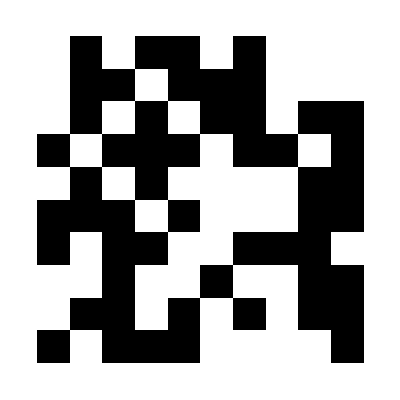

```mathematica
ArrayPlot[RandomInteger[1, {10,10}]]
```

```mathematica
Manipulate[
ArrayPlot[Take[data,h,w]],{{data,RandomInteger[{0,1},{10,20}]},ControlType->None},
{{h,5},1,10,1},{{w,5},1,20,1},Dynamic[Panel[Grid[Outer[Checkbox[Dynamic[data[[#1,#2]]],{0,1}]&,Range[h],Range[w]]]]]]
```

Use the ContinuousAction option to avoid freezing the interface for slow computations:

```mathematica
Manipulate[Pause[1];u,{u,0,1},ContinuousAction->False]
```

Another method for dealing with slow evaluations is setting SynchronousUpdating to False:

```mathematica
Manipulate[Pause[1];u,{u,0,1},SynchronousUpdating->False]
```

The Manipulate documentation page contains over a hundred examples, so go read it to find other cool features!

## Dynamic: what is powering Manipulate?

The Wolfram Language exposes the underlying framework through Dynamic and associated functions:

```mathematica
x=a+b +2
```

2+a+b

```mathematica
Dynamic[Expand[x^2]]
```

The controls can be used separately from the rest:

```mathematica
x=.5
```

0.5

```mathematica
Column[{
Slider[Dynamic[x]],
Dynamic[x]
}]
```

There are many types of controls for many types of data:

```mathematica
visualizer[control_] := DynamicModule[{y},Column[{control[Dynamic[y]],Dynamic[y]}]]
```

```mathematica
visualizer[Slider2D]
```

```mathematica
visualizer[PopupMenu[#, {1,2,3}]&]
```

```mathematica
visualizer[CheckboxBar[#,{1,2,3}]&]
```

```mathematica
RandomImage[]
```

-Graphics-

```mathematica
visualizer[InputField[#, String]&]
```

The full list of control objects can be found here.

The method that automatically chooses a controller in Manipulate can be accessed using Control:

```mathematica
Control[{x,Range[10]}]
```

## Advanced Dynamic

Since Dynamic can wrap any expression you can make two sliders that are linked together, but move in opposite directions:

```mathematica
DynamicModule[{x=0},{Slider[Dynamic[x]],Slider[Dynamic[1-x]]}]
```

Why can’t I move the second controller?

## Advanced Dynamic continued

The reason why you can’t move the second controller is that it’s not in general possible to invert the relation in the first argument:

```mathematica
DynamicModule[{x=0},{Slider[Dynamic[x]],Slider[Dynamic[1-x,(x=1-#)&]]}]
```

For example in this case the function is not invertible and we had to choose a branch:

```mathematica
DynamicModule[{x=0},{Slider[Dynamic[x],{-1,1}],Slider[Dynamic[x^2,Function[x=-Sqrt[#]]],{0,1}]}]
```

## More advanced Dynamic

```mathematica
DynamicModule[{x=0,y}, {Slider[Dynamic[x, (x=#;y=#+1)&]],Dynamic[x],Dynamic[y]}]
```

```mathematica
DynamicModule[{x = {2}},CheckboxBar[Dynamic[x, If[Length[#] > 1, x = Take[#,1], x =#]&],{1,2,3}]]
```